## Fisher Information matrices for functional response models

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/marknovak/Git/general-functional-responses/code/Mathematica

The Fisher information matrix is the Hessian of the negative log-likelihood or, equivalently, the negative Hessian of the log-likelihood.
The Observed Fisher information matrix is the Fisher information matrix evaluated at the MLE.
The Expected Fisher information matrix is the Fisher information matrix “of sample size 1” (Myung et al. 2006, below eqn. 10), i.e. the expectation of the Fisher matrix evaluated over the probability distribution of x_i samples (e.g., x_i \[Distributed] Poisson).  We also take the expectation over the (experiment’s) variables, which in the context of functional responses is Ν and P (and, in the general sense, time T, which we do not do here).
Structural complexity is the natural log of the integration (over all parameters) of the square root of the determinant of the Expected Fisher Information matrix (Myung et al. 2006, 3rd part of RHS of eqn. 10)

### Define function to compute fisher matrix of a function given the vector of its parameters

```mathematica
fisher[fun_,pars_]:=-D[Apply[fun,pars],{pars,2}]
```

#### Test case

```mathematica
f[x_,y_]:=(x^2-y)/(x^2+y^2+1);
fisher[f,{x,y}]//FullSimplify//MatrixForm
```

((2 (-1+3 x^2-y^2) (1+y+y^2))/((1+x^2+y^2)^3) | -(2 x (1+x^2 (1+2 y)-y (2+y (3+2 y))))/((1+x^2+y^2)^3)
-(2 x (1+x^2 (1+2 y)-y (2+y (3+2 y))))/((1+x^2+y^2)^3) | (2 (x^4-3 y+y^3+x^2 (1-3 y (1+y))))/((1+x^2+y^2)^3))

### Functional responses - Number of prey eaten

```mathematica
H1 = a Ν P T;
H2 = (a Ν P T)/(1+a h Ν);
MM=(a Ν P T)/(β+Ν);
BD = (a Ν P T)/(1+a h Ν + γ P);
CM = (a Ν P T)/((1+a h Ν)(1+γ P));
R = (a Ν P T)/P;
HV = (a Ν P T)/P^m;
AG = (a Ν P T)/(P+a h Ν);
AA=(a Ν P T)/(P^m+a h Ν);
```

### Experimental Designs

Temporal duration of experiment:

```mathematica
subs={T-> 1};
```

#### Option 1 - Discrete treatments

```mathematica
Νvals={1,20};
Pvals={1,2};
(* 
Νvals={1,2,4,8,10,15,20}; 
Pvals={1,2,4};
*)
Νprobs=ConstantArray[1/Length[Νvals],Length[Νvals]];
Pprobs=ConstantArray[1/Length[Pvals],Length[Pvals]];
ΝDistE=EmpiricalDistribution[Νprobs->Νvals];
PDistE=EmpiricalDistribution[Pprobs->Pvals];
```

#### Option 2 - Continuous treatments

```mathematica
ΝDist=UniformDistribution[{5,20}];
PDist=UniformDistribution[{1,2}];
```

### Define function for Expected Fisher Matrix given experimental design

AbsoluteTiming[] shows that use of Expectation[] is faster than Integrating over PDF.
AbsoluteTiming[] indicates that it is faster to compute expectations over Ν and P sequentially than to do so simultaneously.
AbsoluteTiming[] also indicates that it is faster to compute expectations over  P before N (but that might be a function of the number or range of N levels versus P levels in the experimental design).

```mathematica
EFisher[FisherMatrix_,func_]:=
Expectation[
Expectation[
Expectation[
FisherMatrix,
x\[Distributed] PoissonDistribution[func]],
P\[Distributed]PDistE], (* Replace option here *)
Ν\[Distributed]ΝDistE] (* Replace option here *)
```

## Fisher information matrices and determinants

#### Likelihood and substitutions

Note: If x_i\[Distributed]Poission(λ_i) for i = 1,...,n are independent and λ = ∑ λ_i, then Y=∑λ_i\[Distributed]Poission(λ).     Therefore we can just replace ∑_(i=1)^n x_i→ x.  
(See https://en.wikipedia.org/wiki/Poisson_distribution#Properties)

See MLE.bias for derivation of logLikelihood
PoislL=-n λ-Log[∏_(i=1)^n x_i!]+Log[λ] ∑_(i=1)^n x_i
The second term (-Log[∏_(i=1)^n x_i!]) drops out in derivative anyway, so leave out.
Expectation will be for a sample size of 1, for substitute here to speed up.

```mathematica
PoislL[func_]:=-n func+Log[func] x/.{n->1}
```

AbsoluteTiming also indicates that performing subB substituting for each part within EFisher speeds things up.

#### Holling Type I model - Poisson

```mathematica
lLH1Poiss[a_]:=PoislL[H1]
FisherH1Poiss=fisher[lLH1Poiss,{a}];
%//FullSimplify//MatrixForm
```

(x/a^2)

```mathematica
EFisherH1Poiss=EFisher[FisherH1Poiss/.subs,H1/.subs];
%//MatrixForm
```

(63/(4 a))

```mathematica
DetH1=Det[EFisherH1Poiss]
```

63/(4 a)

#### Holling Type II model - Poisson

```mathematica
lLH2Poiss[a_,h_]:=PoislL[H2]
FisherH2Poiss=fisher[lLH2Poiss,{a, h}];
%//FullSimplify//MatrixForm
```

((x+3 a h x Ν+2 a^2 h (-P T+h x) Ν^2)/(a^2 (1+a h Ν)^3) | (Ν (x-2 a P T Ν+a h x Ν))/(1+a h Ν)^3
(Ν (x-2 a P T Ν+a h x Ν))/(1+a h Ν)^3 | -(a^2 Ν^2 (x-2 a P T Ν+a h x Ν))/(1+a h Ν)^3)

```mathematica
EFisherH2Poiss=EFisher[FisherH2Poiss/.subs,H2/.subs];
%//FullSimplify//MatrixForm
```

((3 (1/(1+a h)^3+20/(1+20 a h)^3))/(4 a) | a (-3/(4 (1+a h)^3)-300/(1+20 a h)^3)
a (-3/(4 (1+a h)^3)-300/(1+20 a h)^3) | 3/4 a^3 (1/(1+a h)^3+8000/(1+20 a h)^3))

```mathematica
DetH2=Det[EFisherH2Poiss]//FullSimplify
```

(16245 a^2)/(4 (1+a h)^3 (1+20 a h)^3)

#### Michaelis-Menten model - Poisson

```mathematica
lLMMPoiss[a_,β_]:=PoislL[MM]
FisherMMPoiss=fisher[lLMMPoiss,{a, β}];
%//FullSimplify//MatrixForm
```

(x/a^2 | -(P T Ν)/(β+Ν)^2
-(P T Ν)/(β+Ν)^2 | (2 a P T Ν-x (β+Ν))/(β+Ν)^3)

```mathematica
EFisherMMPoiss=EFisher[FisherMMPoiss/.subs,MM/.subs];
%//FullSimplify//MatrixForm
```

((120+63 β)/(80 a+84 a β+4 a β^2) | -3/(4 (1+β)^2)-15/(20+β)^2
-3/(4 (1+β)^2)-15/(20+β)^2 | 3/4 a (1/(1+β)^3+20/(20+β)^3))

```mathematica
DetMM=Det[EFisherMMPoiss]//FullSimplify
```

16245/(4 (1+β)^3 (20+β)^3)

#### Beddington-DeAngelis model - Poisson

```mathematica
lLBDPoiss[a_,h_,γ_]:=PoislL[BD]
FisherBDPoiss=fisher[lLBDPoiss,{a, h,γ}]//FullSimplify;
%//MatrixForm
```

(((1+P γ) (-2 a^2 h P T Ν^2+x (1+P γ+a h Ν) (1+P γ+2 a h Ν)))/(a^2 (1+P γ+a h Ν)^3) | ((1+P γ) Ν (x+P x γ-2 a P T Ν+a h x Ν))/(1+P γ+a h Ν)^3 | (P Ν (-(P T+h x) (1+P γ)+a h (P T-h x) Ν))/(1+P γ+a h Ν)^3
((1+P γ) Ν (x+P x γ-2 a P T Ν+a h x Ν))/(1+P γ+a h Ν)^3 | -(a^2 Ν^2 (x+P x γ-2 a P T Ν+a h x Ν))/(1+P γ+a h Ν)^3 | (a P Ν (2 a P T Ν-x (1+P γ+a h Ν)))/(1+P γ+a h Ν)^3
(P Ν (-(P T+h x) (1+P γ)+a h (P T-h x) Ν))/(1+P γ+a h Ν)^3 | (a P Ν (2 a P T Ν-x (1+P γ+a h Ν)))/(1+P γ+a h Ν)^3 | -(P^2 (x+P x γ-2 a P T Ν+a h x Ν))/(1+P γ+a h Ν)^3)

```mathematica
EFisherBDPoiss=EFisher[FisherBDPoiss/.subs,BD/.subs];
%//FullSimplify//MatrixForm
```

(1/4 (20/(a (1+20 a h+γ))+1/(a+a^2 h+a γ)+2/(a+a^2 h+2 a γ)+40/(a+20 a^2 h+2 a γ)+a h^2 (1/(1+a h+γ)^3+8000/(1+20 a h+γ)^3+2/(1+a h+2 γ)^3+16000/(1+20 a h+2 γ)^3)+h (-2/(1+a h+γ)^2-800/(1+20 a h+γ)^2-4/(1+a h+2 γ)^2-1600/(1+20 a h+2 γ)^2)) | 1/4 a (-1/(1+a h+γ)^2-400/(1+20 a h+γ)^2-2/(1+a h+2 γ)^2-800/(1+20 a h+2 γ)^2+a h (1/(1+a h+γ)^3+8000/(1+20 a h+γ)^3+2/(1+a h+2 γ)^3+16000/(1+20 a h+2 γ)^3)) | -1/(4 (1+a h+γ)^2)-5/(1+20 a h+γ)^2-1/(1+a h+2 γ)^2-20/(1+20 a h+2 γ)^2+1/4 a h (1/(1+a h+γ)^3+400/(1+20 a h+γ)^3+4/(1+a h+2 γ)^3+1600/(1+20 a h+2 γ)^3)
1/4 a (-1/(1+a h+γ)^2-400/(1+20 a h+γ)^2-2/(1+a h+2 γ)^2-800/(1+20 a h+2 γ)^2+a h (1/(1+a h+γ)^3+8000/(1+20 a h+γ)^3+2/(1+a h+2 γ)^3+16000/(1+20 a h+2 γ)^3)) | 1/4 a^3 (1/(1+a h+γ)^3+8000/(1+20 a h+γ)^3+2/(1+a h+2 γ)^3+16000/(1+20 a h+2 γ)^3) | 1/4 a^2 (1/(1+a h+γ)^3+400/(1+20 a h+γ)^3+4/(1+a h+2 γ)^3+1600/(1+20 a h+2 γ)^3)
-1/(4 (1+a h+γ)^2)-5/(1+20 a h+γ)^2-1/(1+a h+2 γ)^2-20/(1+20 a h+2 γ)^2+1/4 a h (1/(1+a h+γ)^3+400/(1+20 a h+γ)^3+4/(1+a h+2 γ)^3+1600/(1+20 a h+2 γ)^3) | 1/4 a^2 (1/(1+a h+γ)^3+400/(1+20 a h+γ)^3+4/(1+a h+2 γ)^3+1600/(1+20 a h+2 γ)^3) | 1/4 a (1/(1+a h+γ)^3+20/(1+20 a h+γ)^3+8/(1+a h+2 γ)^3+160/(1+20 a h+2 γ)^3))

```mathematica
DetBD=Det[EFisherBDPoiss];
%//FullSimplify
```

(5415 a^3 (21+8020 a^3 h^3+420 a^2 h^2 (3+4 γ)+40 a h (3+8 γ+6 γ^2)+14 γ (6+γ (9+5 γ))))/(8 (1+a h+γ)^3 (1+20 a h+γ)^3 (1+a h+2 γ)^3 (1+20 a h+2 γ)^3)

#### Crowley-Martin model - Poisson

```mathematica
lLCMPoiss[a_,h_,γ_]:=PoislL[CM]
FisherCMPoiss=fisher[lLCMPoiss,{a, h,γ}]//FullSimplify;
%//MatrixForm
```

((-(2 h P T Ν^2)/(1+P γ)+(x (1+a h Ν) (1+2 a h Ν))/a^2)/(1+a h Ν)^3 | (Ν (x+a h x Ν-(2 a P T Ν)/(1+P γ)))/(1+a h Ν)^3 | -(P^2 T Ν)/((1+P γ)^2 (1+a h Ν)^2)
(Ν (x+a h x Ν-(2 a P T Ν)/(1+P γ)))/(1+a h Ν)^3 | (a^2 Ν^2 ((2 a P T Ν)/(1+P γ)-x (1+a h Ν)))/(1+a h Ν)^3 | (a^2 P^2 T Ν^2)/((1+P γ)^2 (1+a h Ν)^2)
-(P^2 T Ν)/((1+P γ)^2 (1+a h Ν)^2) | (a^2 P^2 T Ν^2)/((1+P γ)^2 (1+a h Ν)^2) | (P^2 (-x (1+P γ)+(2 a P T Ν)/(1+a h Ν)))/(1+P γ)^3)

```mathematica
EFisherCMPoiss=EFisher[FisherCMPoiss/.subs,CM/.subs];
%//FullSimplify//MatrixForm
```

(((21+20 a h (6+a h (63+401 a h))) (3+4 γ))/(4 a (1+a h)^3 (1+20 a h)^3 (1+γ) (1+2 γ)) | -(a (401+60 a h (21+20 a h (2+7 a h))) (3+4 γ))/(4 (1+a h)^3 (1+20 a h)^3 (1+γ) (1+2 γ)) | -((21+20 a h (4+21 a h)) (5+4 γ (3+2 γ)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2)
-(a (401+60 a h (21+20 a h (2+7 a h))) (3+4 γ))/(4 (1+a h)^3 (1+20 a h)^3 (1+γ) (1+2 γ)) | (a^3 (21+40 a h) (381+20 a h (21+20 a h)) (3+4 γ))/(4 (1+a h)^3 (1+20 a h)^3 (1+γ) (1+2 γ)) | (a^2 (401+40 a h (21+20 a h)) (5+4 γ (3+2 γ)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2)
-((21+20 a h (4+21 a h)) (5+4 γ (3+2 γ)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2) | (a^2 (401+40 a h (21+20 a h)) (5+4 γ (3+2 γ)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2) | (a (21+40 a h) (3+4 γ) (3+6 γ+4 γ^2))/(4 (1+a h) (1+20 a h) (1+γ)^3 (1+2 γ)^3))

```mathematica
DetCM=Det[EFisherCMPoiss];
%//FullSimplify
```

(1805 a^3 (21+40 a h) (3+4 γ))/(8 (1+a h)^4 (1+20 a h)^4 (1+γ)^4 (1+2 γ)^4)

#### Ratio - Poisson

```mathematica
lLRPoiss[a_]:=PoislL[R]
FisherRPoiss=fisher[lLRPoiss,{a}]//FullSimplify;
FisherRPoiss//MatrixForm
```

(x/a^2)

```mathematica
EFisherRPoiss=EFisher[FisherRPoiss/.subs,R/.subs];
%//FullSimplify//MatrixForm
```

(21/(2 a))

```mathematica
DetR=Det[EFisherRPoiss]//FullSimplify
```

21/(2 a)

#### Hassell-Varley - Poisson

```mathematica
lLHVPoiss[a_,m_]:=PoislL[HV]
FisherHVPoiss=fisher[lLHVPoiss,{a,m}]//FullSimplify;
%//MatrixForm
```

(x/a^2 | -P^(1-m) T Ν Log[P]
-P^(1-m) T Ν Log[P] | a P^(1-m) T Ν Log[P]^2)

```mathematica
EFisherHVPoiss=EFisher[FisherHVPoiss/.subs,HV/.subs];
%//FullSimplify//MatrixForm
```

((21 2^(-2-m) (2+2^m))/a | -21 2^(-1-m) Log[2]
-21 2^(-1-m) Log[2] | 21 2^(-1-m) a Log[2]^2)

```mathematica
DetHV=Det[EFisherHVPoiss];
%//FullSimplify
```

441 2^(-3-m) Log[2]^2

#### Arditi-Ginzburg - Poisson

```mathematica
lLAGPoiss[a_,h_]:=PoislL[AG]
FisherAGPoiss=fisher[lLAGPoiss,{a, h}]//FullSimplify;
%//MatrixForm
```

((P (P^2 x+3 a h P x Ν+2 a^2 h (-P T+h x) Ν^2))/(a^2 (P+a h Ν)^3) | (P Ν (a h x Ν+P (x-2 a T Ν)))/(P+a h Ν)^3
(P Ν (a h x Ν+P (x-2 a T Ν)))/(P+a h Ν)^3 | (a^2 Ν^2 (-P x+2 a P T Ν-a h x Ν))/(P+a h Ν)^3)

```mathematica
EFisherAGPoiss=EFisher[FisherAGPoiss/.subs,AG/.subs];
%//FullSimplify//MatrixForm
```

((1/(1+a h)^3+8/(2+a h)^3+20/(1+10 a h)^3+20/(1+20 a h)^3)/(4 a) | a (-1/(4 (1+a h)^3)-1/(2+a h)^3-50/(1+10 a h)^3-100/(1+20 a h)^3)
a (-1/(4 (1+a h)^3)-1/(2+a h)^3-50/(1+10 a h)^3-100/(1+20 a h)^3) | 1/4 a^3 (1/(1+a h)^3+2/(2+a h)^3+2000/(1+10 a h)^3+8000/(1+20 a h)^3))

```mathematica
DetAG=Det[EFisherAGPoiss];
%//FullSimplify
```

(9 a^2 (25889+10 a h (38745+2 a h (231183+a h (1407077+5 a h (504603+50 a h (7749+2362 a h)))))))/(8 (1+a h)^3 (2+a h)^3 (1+10 a h)^3 (1+20 a h)^3)

#### Arditi-Akcakaya model - Poisson

```mathematica
lLAAPoiss[a_,h_,m_]:=PoislL[AA]
FisherAAPoiss=fisher[lLAAPoiss,{a, h,m}]//FullSimplify;
%//MatrixForm
```

((P^m (P^(2 m) x+3 a h P^m x Ν+2 a^2 h (-P T+h x) Ν^2))/(a^2 (P^m+a h Ν)^3) | (P^m Ν (P^m x-2 a P T Ν+a h x Ν))/((P^m+a h Ν)^3) | -(P^m Ν (P^m (P T+h x)+a h (-P T+h x) Ν) Log[P])/((P^m+a h Ν)^3)
(P^m Ν (P^m x-2 a P T Ν+a h x Ν))/((P^m+a h Ν)^3) | -(a^2 Ν^2 (P^m x-2 a P T Ν+a h x Ν))/((P^m+a h Ν)^3) | -(a P^m Ν (P^m x-2 a P T Ν+a h x Ν) Log[P])/((P^m+a h Ν)^3)
-(P^m Ν (P^m (P T+h x)+a h (-P T+h x) Ν) Log[P])/((P^m+a h Ν)^3) | -(a P^m Ν (P^m x-2 a P T Ν+a h x Ν) Log[P])/((P^m+a h Ν)^3) | (a P^m Ν (P^m (P T+h x)+a h (-P T+h x) Ν) Log[P]^2)/((P^m+a h Ν)^3))

```mathematica
EFisherAAPoiss=EFisher[FisherAAPoiss/.subs,AA/.subs];
%//FullSimplify//MatrixForm
```

(1/4 (2 a h^2 (1/((2^m+a h)^3)+8000/((2^m+20 a h)^3))+h (-4/((2^m+a h)^2)-1600/((2^m+20 a h)^2))+(1/(1+a h)^3+2/(2^m+a h)+20/(1+20 a h)^3+40/(2^m+20 a h))/a) | 1/4 a (-1/(1+a h)^3-2/((2^m+a h)^2)-400/(1+20 a h)^3-800/((2^m+20 a h)^2)+2 a h (1/((2^m+a h)^3)+8000/((2^m+20 a h)^3))) | -(2^(-1+2 m) (21 8^m+20 a h (3 2^(1+2 m)+a h (63 2^m+401 a h))) Log[2])/((2^m+a h)^3 (2^m+20 a h)^3)
1/4 a (-1/(1+a h)^3-2/((2^m+a h)^2)-400/(1+20 a h)^3-800/((2^m+20 a h)^2)+2 a h (1/((2^m+a h)^3)+8000/((2^m+20 a h)^3))) | 1/4 a^3 (1/(1+a h)^3+2/((2^m+a h)^3)+8000/(1+20 a h)^3+16000/((2^m+20 a h)^3)) | (2^(-1+m) a^2 (401 8^m+60 a h (21 4^m+20 a h (2^(1+m)+7 a h))) Log[2])/((2^m+a h)^3 (2^m+20 a h)^3)
-(2^(-1+2 m) (21 8^m+20 a h (3 2^(1+2 m)+a h (63 2^m+401 a h))) Log[2])/((2^m+a h)^3 (2^m+20 a h)^3) | (2^(-1+m) a^2 (401 8^m+60 a h (21 4^m+20 a h (2^(1+m)+7 a h))) Log[2])/((2^m+a h)^3 (2^m+20 a h)^3) | (2^(-1+2 m) a (21 8^m+20 a h (3 2^(1+2 m)+a h (63 2^m+401 a h))) Log[2]^2)/((2^m+a h)^3 (2^m+20 a h)^3))

```mathematica
DetAA=Det[EFisherAAPoiss];
%//FullSimplify
```

(5415 2^(-3+2 m) a^3 (7 (2+8^m)+20 a h (2 (2+4^m)+a h (21 (2+2^m)+401 a h))) Log[2]^2)/((1+a h)^3 (2^m+a h)^3 (1+20 a h)^3 (2^m+20 a h)^3)

## Ratios of Determinants

```mathematica
Dets={DetH1,DetH2,DetMM,DetBD,DetCM,DetR,DetHV,DetAG,DetAA};
```

```mathematica
DetRatH1=Dets/DetH1;
%DetRatH1//TableForm
```

1
(3258025 a^6)/(49 (1+a h)^6 (1+20 a h)^6)
(3258025 a^2)/(49 (1+β)^6 (20+β)^6)
(16 a^2 ((((-105-7215 a h-189315 a^2 h^2-2503805 a^3 h^3-21212100 a^4 h^4-148920600 a^5 h^5-662636100 a^6 h^6-1272726000 a^7 h^7-1060920000 a^8 h^8-320800000 a^9 h^9-1512 γ-94878 a h γ-2241540 a^2 h^2 γ-25994754 a^3 h^3 γ-184392180 a^4 h^4 γ-1052086140 a^5 h^5 γ-3702445740 a^6 h^6 γ-5446465200 a^7 h^7 γ-3213000000 a^8 h^8 γ-577440000 a^9 h^9 γ-9702 γ^2-547506 a h γ^2-11451510 a^2 h^2 γ^2-114287346 a^3 h^3 γ^2-661985100 a^4 h^4 γ^2-2945447340 a^5 h^5 γ^2-7629549480 a^6 h^6 γ^2-7435113600 a^7 h^7 γ^2-2192400000 a^8 h^8 γ^2-36540 γ^3-1819296 a h γ^3-32950260 a^2 h^2 γ^3-275636292 a^3 h^3 γ^3-1256645880 a^4 h^4 γ^3-4093985880 a^5 h^5 γ^3-6911573760 a^6 h^6 γ^3-3265214400 a^7 h^7 γ^3-89481 γ^4-3835935 a h γ^4-58382415 a^2 h^2 γ^4-393606377 a^3 h^3 γ^4-1330359660 a^4 h^4 γ^4-2828579760 a^5 h^5 γ^4-2322505920 a^6 h^6 γ^4-148932 γ^5-5322618 a h γ^5-65220120 a^2 h^2 γ^5-332660934 a^3 h^3 γ^5-744539040 a^4 h^4 γ^5-776875680 a^5 h^5 γ^5-170688 γ^6-4861560 a h γ^6-44868600 a^2 h^2 γ^6-154061084 a^3 h^3 γ^6-172020240 a^4 h^4 γ^6-133056 γ^7-2819664 a h γ^7-17388000 a^2 h^2 γ^7-30166632 a^3 h^3 γ^7-67536 γ^8-942768 a h γ^8-2908080 a^2 h^2 γ^8-20160 γ^9-138528 a h γ^9-2688 γ^10) (-(a^3 (24003+1584369 a h+37819089 a^2 h^2+387415083 a^3 h^3+1621854360 a^4 h^4+3558402000 a^5 h^5+4667544000 a^6 h^6+3810240000 a^7 h^7+1814400000 a^8 h^8+384000000 a^9 h^9+312039 γ+18460245 a h γ+389231073 a^2 h^2 γ+3450237567 a^3 h^3 γ+12078038700 a^4 h^4 γ+21210900000 a^5 h^5 γ+20771856000 a^6 h^6 γ+11180640000 a^7 h^7 γ+2620800000 a^8 h^8 γ+1800225 γ^2+93333411 a h γ^2+1692537525 a^2 h^2 γ^2+12570615459 a^3 h^3 γ^2+35279208720 a^4 h^4 γ^2+46511949600 a^5 h^5 γ^2+30400272000 a^6 h^6 γ^2+8197920000 a^7 h^7 γ^2+6056757 γ^3+267589941 a h γ^3+4029943743 a^2 h^2 γ^3+23960463089 a^3 h^3 γ^3+50463490140 a^4 h^4 γ^3+44413450800 a^5 h^5 γ^3+14612472000 a^6 h^6 γ^3+13105638 γ^4+476032500 a h γ^4+5674375350 a^2 h^2 γ^4+25190298918 a^3 h^3 γ^4+35332128720 a^4 h^4 γ^4+15576127200 a^5 h^5 γ^4+18914364 γ^5+538163322 a h γ^5+4726240596 a^2 h^2 γ^5+13856656668 a^3 h^3 γ^5+9692670960 a^4 h^4 γ^5+18194274 γ^6+377520084 a h γ^6+2157120504 a^2 h^2 γ^6+3119043864 a^3 h^3 γ^6+11233404 γ^7+150184200 a h γ^7+416437056 a^2 h^2 γ^7+4032504 γ^8+25927344 a h γ^8+640080 γ^9) (-105-7215 a h-189315 a^2 h^2-2503805 a^3 h^3-21212100 a^4 h^4-148920600 a^5 h^5-662636100 a^6 h^6-1272726000 a^7 h^7-1060920000 a^8 h^8-320800000 a^9 h^9-1512 γ-94878 a h γ-2241540 a^2 h^2 γ-25994754 a^3 h^3 γ-184392180 a^4 h^4 γ-1052086140 a^5 h^5 γ-3702445740 a^6 h^6 γ-5446465200 a^7 h^7 γ-3213000000 a^8 h^8 γ-577440000 a^9 h^9 γ-9702 γ^2-547506 a h γ^2-11451510 a^2 h^2 γ^2-114287346 a^3 h^3 γ^2-661985100 a^4 h^4 γ^2-2945447340 a^5 h^5 γ^2-7629549480 a^6 h^6 γ^2-7435113600 a^7 h^7 γ^2-2192400000 a^8 h^8 γ^2-36540 γ^3-1819296 a h γ^3-32950260 a^2 h^2 γ^3-275636292 a^3 h^3 γ^3-1256645880 a^4 h^4 γ^3-4093985880 a^5 h^5 γ^3-6911573760 a^6 h^6 γ^3-3265214400 a^7 h^7 γ^3-89481 γ^4-3835935 a h γ^4-58382415 a^2 h^2 γ^4-393606377 a^3 h^3 γ^4-1330359660 a^4 h^4 γ^4-2828579760 a^5 h^5 γ^4-2322505920 a^6 h^6 γ^4-148932 γ^5-5322618 a h γ^5-65220120 a^2 h^2 γ^5-332660934 a^3 h^3 γ^5-744539040 a^4 h^4 γ^5-776875680 a^5 h^5 γ^5-170688 γ^6-4861560 a h γ^6-44868600 a^2 h^2 γ^6-154061084 a^3 h^3 γ^6-172020240 a^4 h^4 γ^6-133056 γ^7-2819664 a h γ^7-17388000 a^2 h^2 γ^7-30166632 a^3 h^3 γ^7-67536 γ^8-942768 a h γ^8-2908080 a^2 h^2 γ^8-20160 γ^9-138528 a h γ^9-2688 γ^10))/(16 (1+a h+γ)^6 (1+20 a h+γ)^6 (1+a h+2 γ)^6 (1+20 a h+2 γ)^6)+(a^2 (2005+132615 a h+3181815 a^2 h^2+33131805 a^3 h^3+148920600 a^4 h^4+424242000 a^5 h^5+1001522000 a^6 h^6+1514520000 a^7 h^7+1154400000 a^8 h^8+336000000 a^9 h^9+25263 γ+1508031 a h γ+32201973 a^2 h^2 γ+291975705 a^3 h^3 γ+1092370500 a^4 h^4 γ+2421241200 a^5 h^5 γ+4024015200 a^6 h^6 γ+3876768000 a^7 h^7 γ+1442880000 a^8 h^8 γ+140751 γ^2+7422723 a h γ^2+137523537 a^2 h^2 γ^2+1052827965 a^3 h^3 γ^2+3153583200 a^4 h^4 γ^2+5168318400 a^5 h^5 γ^2+5572233600 a^6 h^6 γ^2+2634912000 a^7 h^7 γ^2+455937 γ^3+20673009 a h γ^3+321230079 a^2 h^2 γ^3+1986462135 a^3 h^3 γ^3+4473512100 a^4 h^4 γ^3+4885045200 a^5 h^5 γ^3+2661532800 a^6 h^6 γ^3+947964 γ^4+35667450 a h γ^4+443348364 a^2 h^2 γ^4+2067823170 a^3 h^3 γ^4+3117118800 a^4 h^4 γ^4+1725343200 a^5 h^5 γ^4+1313676 γ^5+39072348 a h γ^5+361782288 a^2 h^2 γ^5+1126685700 a^3 h^3 γ^5+854269200 a^4 h^4 γ^5+1214228 γ^6+26558280 a h γ^6+161763648 a^2 h^2 γ^6+251349000 a^3 h^3 γ^6+721800 γ^7+10245312 a h γ^7+30603024 a^2 h^2 γ^7+250224 γ^8+1717632 a h γ^8+38496 γ^9) (-1203 a-79569 a^2 h-1909089 a^3 h^2-19879083 a^4 h^3-89352360 a^5 h^4-254545200 a^6 h^5-600913200 a^7 h^6-908712000 a^8 h^7-692640000 a^9 h^8-201600000 a^10 h^9-17644 a γ-1059660 a^2 h γ-22824888 a^3 h^2 γ-209973372 a^4 h^3 γ-810885300 a^5 h^4 γ-1910109600 a^6 h^5 γ-3544686800 a^7 h^6 γ-4018392000 a^8 h^7 γ-2097120000 a^9 h^8 γ-336000000 a^10 h^9 γ-115488 a γ^2-6195042 a^2 h γ^2-117613098 a^3 h^2 γ^2-936093564 a^4 h^3 γ^2-3023774820 a^5 h^4 γ^2-5671285200 a^6 h^5 γ^2-7753622400 a^7 h^6 γ^2-5724432000 a^8 h^7 γ^2-1442880000 a^9 h^8 γ^2-444308 a γ^3-20861064 a^2 h γ^3-340920480 a^3 h^2 γ^3-2281288254 a^4 h^3 γ^3-5925127740 a^5 h^4 γ^3-8323938000 a^6 h^5 γ^3-7464965600 a^7 h^6 γ^3-2634912000 a^8 h^7 γ^3-1112775 a γ^4-44581509 a^2 h γ^4-607737429 a^3 h^2 γ^4-3279989853 a^4 h^3 γ^4-6429450420 a^5 h^4 γ^4-6033560400 a^6 h^5 γ^4-2661532800 a^7 h^6 γ^4-1895928 a γ^5-62700372 a^2 h γ^5-682138560 a^3 h^2 γ^5-2781237438 a^4 h^3 γ^5-3660833760 a^5 h^4 γ^5-1725343200 a^6 h^5 γ^5-2225550 a γ^6-58039632 a^2 h γ^6-470869992 a^3 h^2 γ^6-1287885564 a^4 h^3 γ^6-854269200 a^5 h^4 γ^6-1777232 a γ^7-34105680 a^2 h γ^7-182848704 a^3 h^2 γ^7-251349000 a^4 h^3 γ^7-923904 a γ^8-11548656 a^2 h γ^8-30603024 a^3 h^2 γ^8-282304 a γ^9-1717632 a^2 h γ^9-38496 a γ^10))/(16 (1+a h+γ)^6 (1+20 a h+γ)^6 (1+a h+2 γ)^6 (1+20 a h+2 γ)^6)))/(4 (1+a h+γ)^3 (1+20 a h+γ)^3 (1+a h+2 γ)^3 (1+20 a h+2 γ)^3)-(a^2 (2005+132615 a h+3181815 a^2 h^2+33131805 a^3 h^3+148920600 a^4 h^4+424242000 a^5 h^5+1001522000 a^6 h^6+1514520000 a^7 h^7+1154400000 a^8 h^8+336000000 a^9 h^9+25263 γ+1508031 a h γ+32201973 a^2 h^2 γ+291975705 a^3 h^3 γ+1092370500 a^4 h^4 γ+2421241200 a^5 h^5 γ+4024015200 a^6 h^6 γ+3876768000 a^7 h^7 γ+1442880000 a^8 h^8 γ+140751 γ^2+7422723 a h γ^2+137523537 a^2 h^2 γ^2+1052827965 a^3 h^3 γ^2+3153583200 a^4 h^4 γ^2+5168318400 a^5 h^5 γ^2+5572233600 a^6 h^6 γ^2+2634912000 a^7 h^7 γ^2+455937 γ^3+20673009 a h γ^3+321230079 a^2 h^2 γ^3+1986462135 a^3 h^3 γ^3+4473512100 a^4 h^4 γ^3+4885045200 a^5 h^5 γ^3+2661532800 a^6 h^6 γ^3+947964 γ^4+35667450 a h γ^4+443348364 a^2 h^2 γ^4+2067823170 a^3 h^3 γ^4+3117118800 a^4 h^4 γ^4+1725343200 a^5 h^5 γ^4+1313676 γ^5+39072348 a h γ^5+361782288 a^2 h^2 γ^5+1126685700 a^3 h^3 γ^5+854269200 a^4 h^4 γ^5+1214228 γ^6+26558280 a h γ^6+161763648 a^2 h^2 γ^6+251349000 a^3 h^3 γ^6+721800 γ^7+10245312 a h γ^7+30603024 a^2 h^2 γ^7+250224 γ^8+1717632 a h γ^8+38496 γ^9) (-((-105-7215 a h-189315 a^2 h^2-2503805 a^3 h^3-21212100 a^4 h^4-148920600 a^5 h^5-662636100 a^6 h^6-1272726000 a^7 h^7-1060920000 a^8 h^8-320800000 a^9 h^9-1512 γ-94878 a h γ-2241540 a^2 h^2 γ-25994754 a^3 h^3 γ-184392180 a^4 h^4 γ-1052086140 a^5 h^5 γ-3702445740 a^6 h^6 γ-5446465200 a^7 h^7 γ-3213000000 a^8 h^8 γ-577440000 a^9 h^9 γ-9702 γ^2-547506 a h γ^2-11451510 a^2 h^2 γ^2-114287346 a^3 h^3 γ^2-661985100 a^4 h^4 γ^2-2945447340 a^5 h^5 γ^2-7629549480 a^6 h^6 γ^2-7435113600 a^7 h^7 γ^2-2192400000 a^8 h^8 γ^2-36540 γ^3-1819296 a h γ^3-32950260 a^2 h^2 γ^3-275636292 a^3 h^3 γ^3-1256645880 a^4 h^4 γ^3-4093985880 a^5 h^5 γ^3-6911573760 a^6 h^6 γ^3-3265214400 a^7 h^7 γ^3-89481 γ^4-3835935 a h γ^4-58382415 a^2 h^2 γ^4-393606377 a^3 h^3 γ^4-1330359660 a^4 h^4 γ^4-2828579760 a^5 h^5 γ^4-2322505920 a^6 h^6 γ^4-148932 γ^5-5322618 a h γ^5-65220120 a^2 h^2 γ^5-332660934 a^3 h^3 γ^5-744539040 a^4 h^4 γ^5-776875680 a^5 h^5 γ^5-170688 γ^6-4861560 a h γ^6-44868600 a^2 h^2 γ^6-154061084 a^3 h^3 γ^6-172020240 a^4 h^4 γ^6-133056 γ^7-2819664 a h γ^7-17388000 a^2 h^2 γ^7-30166632 a^3 h^3 γ^7-67536 γ^8-942768 a h γ^8-2908080 a^2 h^2 γ^8-20160 γ^9-138528 a h γ^9-2688 γ^10) (-1203 a-79569 a^2 h-1909089 a^3 h^2-19879083 a^4 h^3-89352360 a^5 h^4-254545200 a^6 h^5-600913200 a^7 h^6-908712000 a^8 h^7-692640000 a^9 h^8-201600000 a^10 h^9-17644 a γ-1059660 a^2 h γ-22824888 a^3 h^2 γ-209973372 a^4 h^3 γ-810885300 a^5 h^4 γ-1910109600 a^6 h^5 γ-3544686800 a^7 h^6 γ-4018392000 a^8 h^7 γ-2097120000 a^9 h^8 γ-336000000 a^10 h^9 γ-115488 a γ^2-6195042 a^2 h γ^2-117613098 a^3 h^2 γ^2-936093564 a^4 h^3 γ^2-3023774820 a^5 h^4 γ^2-5671285200 a^6 h^5 γ^2-7753622400 a^7 h^6 γ^2-5724432000 a^8 h^7 γ^2-1442880000 a^9 h^8 γ^2-444308 a γ^3-20861064 a^2 h γ^3-340920480 a^3 h^2 γ^3-2281288254 a^4 h^3 γ^3-5925127740 a^5 h^4 γ^3-8323938000 a^6 h^5 γ^3-7464965600 a^7 h^6 γ^3-2634912000 a^8 h^7 γ^3-1112775 a γ^4-44581509 a^2 h γ^4-607737429 a^3 h^2 γ^4-3279989853 a^4 h^3 γ^4-6429450420 a^5 h^4 γ^4-6033560400 a^6 h^5 γ^4-2661532800 a^7 h^6 γ^4-1895928 a γ^5-62700372 a^2 h γ^5-682138560 a^3 h^2 γ^5-2781237438 a^4 h^3 γ^5-3660833760 a^5 h^4 γ^5-1725343200 a^6 h^5 γ^5-2225550 a γ^6-58039632 a^2 h γ^6-470869992 a^3 h^2 γ^6-1287885564 a^4 h^3 γ^6-854269200 a^5 h^4 γ^6-1777232 a γ^7-34105680 a^2 h γ^7-182848704 a^3 h^2 γ^7-251349000 a^4 h^3 γ^7-923904 a γ^8-11548656 a^2 h γ^8-30603024 a^3 h^2 γ^8-282304 a γ^9-1717632 a^2 h γ^9-38496 a γ^10))/(16 (1+a h+γ)^6 (1+20 a h+γ)^6 (1+a h+2 γ)^6 (1+20 a h+2 γ)^6)+(a (2005+132615 a h+3181815 a^2 h^2+33131805 a^3 h^3+148920600 a^4 h^4+424242000 a^5 h^5+1001522000 a^6 h^6+1514520000 a^7 h^7+1154400000 a^8 h^8+336000000 a^9 h^9+25263 γ+1508031 a h γ+32201973 a^2 h^2 γ+291975705 a^3 h^3 γ+1092370500 a^4 h^4 γ+2421241200 a^5 h^5 γ+4024015200 a^6 h^6 γ+3876768000 a^7 h^7 γ+1442880000 a^8 h^8 γ+140751 γ^2+7422723 a h γ^2+137523537 a^2 h^2 γ^2+1052827965 a^3 h^3 γ^2+3153583200 a^4 h^4 γ^2+5168318400 a^5 h^5 γ^2+5572233600 a^6 h^6 γ^2+2634912000 a^7 h^7 γ^2+455937 γ^3+20673009 a h γ^3+321230079 a^2 h^2 γ^3+1986462135 a^3 h^3 γ^3+4473512100 a^4 h^4 γ^3+4885045200 a^5 h^5 γ^3+2661532800 a^6 h^6 γ^3+947964 γ^4+35667450 a h γ^4+443348364 a^2 h^2 γ^4+2067823170 a^3 h^3 γ^4+3117118800 a^4 h^4 γ^4+1725343200 a^5 h^5 γ^4+1313676 γ^5+39072348 a h γ^5+361782288 a^2 h^2 γ^5+1126685700 a^3 h^3 γ^5+854269200 a^4 h^4 γ^5+1214228 γ^6+26558280 a h γ^6+161763648 a^2 h^2 γ^6+251349000 a^3 h^3 γ^6+721800 γ^7+10245312 a h γ^7+30603024 a^2 h^2 γ^7+250224 γ^8+1717632 a h γ^8+38496 γ^9) (63+4329 a h+113589 a^2 h^2+1502283 a^3 h^3+12727260 a^4 h^4+89352360 a^5 h^5+397581660 a^6 h^6+763635600 a^7 h^7+636552000 a^8 h^8+192480000 a^9 h^9+1029 γ+64815 a h γ+1542303 a^2 h^2 γ+18179377 a^3 h^3 γ+133585200 a^4 h^4 γ+797457180 a^5 h^5 γ+2957002440 a^6 h^6 γ+4615485600 a^7 h^7 γ+2980656000 a^8 h^8 γ+641600000 a^9 h^9 γ+7560 γ^2+431460 a h γ^2+9197118 a^2 h^2 γ^2+95275638 a^3 h^3 γ^2+594616680 a^4 h^4 γ^2+2923063920 a^5 h^5 γ^2+8608220460 a^6 h^6 γ^2+10132174800 a^7 h^7 γ^2+4516344000 a^8 h^8 γ^2+577440000 a^9 h^9 γ^2+32970 γ^3+1680870 a h γ^3+31597650 a^2 h^2 γ^3+282314660 a^3 h^3 γ^3+1454608260 a^4 h^4 γ^3+5630767500 a^5 h^5 γ^3+12250202160 a^6 h^6 γ^3+9543619200 a^7 h^7 γ^3+2192400000 a^8 h^8 γ^3+94815 γ^4+4242465 a h γ^4+68894469 a^2 h^2 γ^4+517046205 a^3 h^3 γ^4+2111421060 a^4 h^4 γ^4+6011227440 a^5 h^5 γ^4+8523572400 a^6 h^6 γ^4+3265214400 a^7 h^7 γ^4+188769 γ^5+7247187 a h γ^5+98830935 a^2 h^2 γ^5+599022935 a^3 h^3 γ^5+1817941860 a^4 h^4 γ^5+3372294720 a^5 h^5 γ^5+2322505920 a^6 h^6 γ^5+265482 γ^6+8484930 a h γ^6+93261672 a^2 h^2 γ^6+428514618 a^3 h^3 γ^6+859390560 a^4 h^4 γ^6+776875680 a^5 h^5 γ^6+263760 γ^7+6723480 a h γ^7+55823544 a^2 h^2 γ^7+172988404 a^3 h^3 γ^7+172020240 a^4 h^4 γ^7+181440 γ^8+3451680 a h γ^8+19235664 a^2 h^2 γ^8+30166632 a^3 h^3 γ^8+82320 γ^9+1037040 a h γ^9+2908080 a^2 h^2 γ^9+22176 γ^10+138528 a h γ^10+2688 γ^11))/(16 (1+a h+γ)^6 (1+20 a h+γ)^6 (1+a h+2 γ)^6 (1+20 a h+2 γ)^6)))/(4 (1+a h+γ)^3 (1+20 a h+γ)^3 (1+a h+2 γ)^3 (1+20 a h+2 γ)^3)+(a (189+12987 a h+340767 a^2 h^2+4506849 a^3 h^3+38181780 a^4 h^4+268057080 a^5 h^5+1192744980 a^6 h^6+2290906800 a^7 h^7+1909656000 a^8 h^8+577440000 a^9 h^9+2331 γ+144903 a h γ+3374973 a^2 h^2 γ+38120181 a^3 h^3 γ+256309200 a^4 h^4 γ+1352855220 a^5 h^5 γ+4265641800 a^6 h^6 γ+5326608000 a^7 h^7 γ+2192400000 a^8 h^8 γ+12663 γ^2+698427 a h γ^2+14120001 a^2 h^2 γ^2+132915537 a^3 h^3 γ^2+688999500 a^4 h^4 γ^2+2603878920 a^5 h^5 γ^2+5299575120 a^6 h^6 γ^2+3265214400 a^7 h^7 γ^2+39837 γ^3+1901085 a h γ^3+32351571 a^2 h^2 γ^3+244441967 a^3 h^3 γ^3+929044620 a^4 h^4 γ^3+2284864800 a^5 h^5 γ^3+2322505920 a^6 h^6 γ^3+80136 γ^4+3199950 a h γ^4+43864632 a^2 h^2 γ^4+250114914 a^3 h^3 γ^4+629687520 a^4 h^4 γ^4+776875680 a^5 h^5 γ^4+107100 γ^5+3415200 a h γ^5+35231112 a^2 h^2 γ^5+135133764 a^3 h^3 γ^5+172020240 a^4 h^4 γ^5+95256 γ^6+2259792 a h γ^6+15540336 a^2 h^2 γ^6+30166632 a^3 h^3 γ^6+54432 γ^7+848496 a h γ^7+2908080 a^2 h^2 γ^7+18144 γ^8+138528 a h γ^8+2688 γ^9) (-((-1203 a-79569 a^2 h-1909089 a^3 h^2-19879083 a^4 h^3-89352360 a^5 h^4-254545200 a^6 h^5-600913200 a^7 h^6-908712000 a^8 h^7-692640000 a^9 h^8-201600000 a^10 h^9-17644 a γ-1059660 a^2 h γ-22824888 a^3 h^2 γ-209973372 a^4 h^3 γ-810885300 a^5 h^4 γ-1910109600 a^6 h^5 γ-3544686800 a^7 h^6 γ-4018392000 a^8 h^7 γ-2097120000 a^9 h^8 γ-336000000 a^10 h^9 γ-115488 a γ^2-6195042 a^2 h γ^2-117613098 a^3 h^2 γ^2-936093564 a^4 h^3 γ^2-3023774820 a^5 h^4 γ^2-5671285200 a^6 h^5 γ^2-7753622400 a^7 h^6 γ^2-5724432000 a^8 h^7 γ^2-1442880000 a^9 h^8 γ^2-444308 a γ^3-20861064 a^2 h γ^3-340920480 a^3 h^2 γ^3-2281288254 a^4 h^3 γ^3-5925127740 a^5 h^4 γ^3-8323938000 a^6 h^5 γ^3-7464965600 a^7 h^6 γ^3-2634912000 a^8 h^7 γ^3-1112775 a γ^4-44581509 a^2 h γ^4-607737429 a^3 h^2 γ^4-3279989853 a^4 h^3 γ^4-6429450420 a^5 h^4 γ^4-6033560400 a^6 h^5 γ^4-2661532800 a^7 h^6 γ^4-1895928 a γ^5-62700372 a^2 h γ^5-682138560 a^3 h^2 γ^5-2781237438 a^4 h^3 γ^5-3660833760 a^5 h^4 γ^5-1725343200 a^6 h^5 γ^5-2225550 a γ^6-58039632 a^2 h γ^6-470869992 a^3 h^2 γ^6-1287885564 a^4 h^3 γ^6-854269200 a^5 h^4 γ^6-1777232 a γ^7-34105680 a^2 h γ^7-182848704 a^3 h^2 γ^7-251349000 a^4 h^3 γ^7-923904 a γ^8-11548656 a^2 h γ^8-30603024 a^3 h^2 γ^8-282304 a γ^9-1717632 a^2 h γ^9-38496 a γ^10)^2)/(16 (1+a h+γ)^6 (1+20 a h+γ)^6 (1+a h+2 γ)^6 (1+20 a h+2 γ)^6)+(a^2 (24003+1584369 a h+37819089 a^2 h^2+387415083 a^3 h^3+1621854360 a^4 h^4+3558402000 a^5 h^5+4667544000 a^6 h^6+3810240000 a^7 h^7+1814400000 a^8 h^8+384000000 a^9 h^9+312039 γ+18460245 a h γ+389231073 a^2 h^2 γ+3450237567 a^3 h^3 γ+12078038700 a^4 h^4 γ+21210900000 a^5 h^5 γ+20771856000 a^6 h^6 γ+11180640000 a^7 h^7 γ+2620800000 a^8 h^8 γ+1800225 γ^2+93333411 a h γ^2+1692537525 a^2 h^2 γ^2+12570615459 a^3 h^3 γ^2+35279208720 a^4 h^4 γ^2+46511949600 a^5 h^5 γ^2+30400272000 a^6 h^6 γ^2+8197920000 a^7 h^7 γ^2+6056757 γ^3+267589941 a h γ^3+4029943743 a^2 h^2 γ^3+23960463089 a^3 h^3 γ^3+50463490140 a^4 h^4 γ^3+44413450800 a^5 h^5 γ^3+14612472000 a^6 h^6 γ^3+13105638 γ^4+476032500 a h γ^4+5674375350 a^2 h^2 γ^4+25190298918 a^3 h^3 γ^4+35332128720 a^4 h^4 γ^4+15576127200 a^5 h^5 γ^4+18914364 γ^5+538163322 a h γ^5+4726240596 a^2 h^2 γ^5+13856656668 a^3 h^3 γ^5+9692670960 a^4 h^4 γ^5+18194274 γ^6+377520084 a h γ^6+2157120504 a^2 h^2 γ^6+3119043864 a^3 h^3 γ^6+11233404 γ^7+150184200 a h γ^7+416437056 a^2 h^2 γ^7+4032504 γ^8+25927344 a h γ^8+640080 γ^9) (63+4329 a h+113589 a^2 h^2+1502283 a^3 h^3+12727260 a^4 h^4+89352360 a^5 h^5+397581660 a^6 h^6+763635600 a^7 h^7+636552000 a^8 h^8+192480000 a^9 h^9+1029 γ+64815 a h γ+1542303 a^2 h^2 γ+18179377 a^3 h^3 γ+133585200 a^4 h^4 γ+797457180 a^5 h^5 γ+2957002440 a^6 h^6 γ+4615485600 a^7 h^7 γ+2980656000 a^8 h^8 γ+641600000 a^9 h^9 γ+7560 γ^2+431460 a h γ^2+9197118 a^2 h^2 γ^2+95275638 a^3 h^3 γ^2+594616680 a^4 h^4 γ^2+2923063920 a^5 h^5 γ^2+8608220460 a^6 h^6 γ^2+10132174800 a^7 h^7 γ^2+4516344000 a^8 h^8 γ^2+577440000 a^9 h^9 γ^2+32970 γ^3+1680870 a h γ^3+31597650 a^2 h^2 γ^3+282314660 a^3 h^3 γ^3+1454608260 a^4 h^4 γ^3+5630767500 a^5 h^5 γ^3+12250202160 a^6 h^6 γ^3+9543619200 a^7 h^7 γ^3+2192400000 a^8 h^8 γ^3+94815 γ^4+4242465 a h γ^4+68894469 a^2 h^2 γ^4+517046205 a^3 h^3 γ^4+2111421060 a^4 h^4 γ^4+6011227440 a^5 h^5 γ^4+8523572400 a^6 h^6 γ^4+3265214400 a^7 h^7 γ^4+188769 γ^5+7247187 a h γ^5+98830935 a^2 h^2 γ^5+599022935 a^3 h^3 γ^5+1817941860 a^4 h^4 γ^5+3372294720 a^5 h^5 γ^5+2322505920 a^6 h^6 γ^5+265482 γ^6+8484930 a h γ^6+93261672 a^2 h^2 γ^6+428514618 a^3 h^3 γ^6+859390560 a^4 h^4 γ^6+776875680 a^5 h^5 γ^6+263760 γ^7+6723480 a h γ^7+55823544 a^2 h^2 γ^7+172988404 a^3 h^3 γ^7+172020240 a^4 h^4 γ^7+181440 γ^8+3451680 a h γ^8+19235664 a^2 h^2 γ^8+30166632 a^3 h^3 γ^8+82320 γ^9+1037040 a h γ^9+2908080 a^2 h^2 γ^9+22176 γ^10+138528 a h γ^10+2688 γ^11))/(16 (1+a h+γ)^6 (1+20 a h+γ)^6 (1+a h+2 γ)^6 (1+20 a h+2 γ)^6)))/(4 (1+a h+γ)^3 (1+20 a h+γ)^3 (1+a h+2 γ)^3 (1+20 a h+2 γ)^3)))^2)/3969
(16 a^2 ((a (21+40 a h) (9+30 γ+36 γ^2+16 γ^3) (-(a^2 (401+1260 a h+2400 a^2 h^2+8400 a^3 h^3)^2 (3+4 γ)^2)/(16 (1+a h)^6 (1+20 a h)^6 (1+γ)^2 (1+2 γ)^2)+(a^2 (21+120 a h+1260 a^2 h^2+8020 a^3 h^3) (8001+24060 a h+25200 a^2 h^2+16000 a^3 h^3) (3+4 γ)^2)/(16 (1+a h)^6 (1+20 a h)^6 (1+γ)^2 (1+2 γ)^2)))/(4 (1+a h) (1+20 a h) (1+γ)^3 (1+2 γ)^3)-(a^2 (401+840 a h+800 a^2 h^2) (5+12 γ+8 γ^2) ((a (401+840 a h+800 a^2 h^2) (21+120 a h+1260 a^2 h^2+8020 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)-(a (21+80 a h+420 a^2 h^2) (401+1260 a h+2400 a^2 h^2+8400 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2)-((21+80 a h+420 a^2 h^2) (5+12 γ+8 γ^2) (-(a^3 (401+840 a h+800 a^2 h^2) (401+1260 a h+2400 a^2 h^2+8400 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)+(a^3 (21+80 a h+420 a^2 h^2) (8001+24060 a h+25200 a^2 h^2+16000 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2))^2)/3969
4/9
49 2^(-2-2 m) a^2 Log[2]^4
(16 a^2 ((233001 a^2)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(51011289 a^3 h)/(2 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(4945320513 a^4 h^2)/(4 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(283583608623 a^5 h^3)/(8 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(5434697647053 a^6 h^4)/(8 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(74400321589209 a^7 h^5)/(8 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(751132393803261 a^8 h^6)/(8 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(700894771451910 a^9 h^7)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(7593814941219045 a^10 h^8)/(2 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(14534543212534170 a^11 h^9)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(77255394561186525 a^12 h^10)/(2 (1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(71595267397384500 a^13 h^11)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(93622329198866250 a^14 h^12)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(86935445069287500 a^15 h^13)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(57032261662500000 a^16 h^14)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(25847644646250000 a^17 h^15)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(7696218375000000 a^18 h^16)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(1353145500000000 a^19 h^17)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6)+(106290000000000 a^20 h^18)/((1+a h)^6 (2+a h)^6 (1+10 a h)^6 (1+20 a h)^6))^2)/3969
(16 a^2 (((2^(-1+2 m) a (21 2^(3 m)+15 2^(3+2 m) a h+315 2^(2+m) a^2 h^2+8020 a^3 h^3) (-(a^2 (401 2^(6 m)+401 2^(1+4 m)+25263 2^(5 m) a h+315 2^(3+3 m) a h+25263 2^(1+4 m) a h+315 2^(2+6 m) a h+1663749 2^(4 m) a^2 h^2+75 2^(6+2 m) a^2 h^2+19845 2^(3+3 m) a^2 h^2+19845 2^(2+5 m) a^2 h^2+75 2^(5+6 m) a^2 h^2+8209341 2^(3 m) a^3 h^3+525 2^(5+m) a^3 h^3+4725 2^(6+2 m) a^3 h^3+5595471 2^(1+4 m) a^3 h^3+4725 2^(5+5 m) a^3 h^3+525 2^(4+6 m) a^3 h^3+33075 2^(5+m) a^4 h^4+4432515 2^(2+2 m) a^4 h^4+11133045 2^(2+3 m) a^4 h^4+3187815 2^(3+4 m) a^4 h^4+33075 2^(4+5 m) a^4 h^4+2083725 2^(4+m) a^5 h^5+5712525 2^(4+2 m) a^5 h^5+382725 2^(8+3 m) a^5 h^5+1989225 2^(4+4 m) a^5 h^5+3208000 a^6 h^6+7177275 2^(5+m) a^6 h^6+1555875 2^(7+2 m) a^6 h^6+10154025 2^(4+3 m) a^6 h^6+50125 2^(7+4 m) a^6 h^6+10080000 a^7 h^7+4102875 2^(7+m) a^7 h^7+5520375 2^(6+2 m) a^7 h^7+39375 2^(9+3 m) a^7 h^7+19200000 a^8 h^8+2480625 2^(8+m) a^8 h^8+9375 2^(12+2 m) a^8 h^8+67200000 a^9 h^9+65625 2^(11+m) a^9 h^9)^2)/(16 (1+a h)^6 (2^m+a h)^6 (1+20 a h)^6 (2^m+20 a h)^6)+(a^2 (8001 2^(6 m)+8001 2^(1+3 m)+504063 2^(5 m) a h+6015 2^(3+2 m) a h+504063 2^(1+3 m) a h+6015 2^(2+6 m) a h+11065383 2^(4 m) a^2 h^2+1575 2^(5+m) a^2 h^2+378945 2^(3+2 m) a^2 h^2+11065383 2^(1+3 m) a^2 h^2+378945 2^(2+5 m) a^2 h^2+1575 2^(4+6 m) a^2 h^2+32000 a^3 h^3+282779343 2^(3 m) a^3 h^3+99225 2^(5+m) a^3 h^3+8318745 2^(3+2 m) a^3 h^3+8318745 2^(2+4 m) a^3 h^3+99225 2^(4+5 m) a^3 h^3+125 2^(7+6 m) a^3 h^3+2016000 a^4 h^4+2178225 2^(5+m) a^4 h^4+197052345 2^(2+2 m) a^4 h^4+181516545 2^(2+3 m) a^4 h^4+2178225 2^(4+4 m) a^4 h^4+7875 2^(7+5 m) a^4 h^4+44256000 a^5 h^5+49711725 2^(4+m) a^5 h^5+124781175 2^(4+2 m) a^5 h^5+43758225 2^(4+3 m) a^5 h^5+172875 2^(7+4 m) a^5 h^5+441000000 a^6 h^6+31255875 2^(6+m) a^6 h^6+29838375 2^(6+2 m) a^6 h^6+1236375 2^(8+3 m) a^6 h^6+1077600000 a^7 h^7+7441875 2^(8+m) a^7 h^7+808125 2^(10+2 m) a^7 h^7+1008000000 a^8 h^8+196875 2^(12+m) a^8 h^8+384000000 a^9 h^9) (21 2^(6 m)+21 2^(1+5 m)+3969 2^(5 m) a h+15 2^(4+4 m) a h+15 2^(3+6 m) a h+44163 2^(4 m) a^2 h^2+315 2^(3+3 m) a^2 h^2+32823 2^(1+5 m) a^2 h^2+315 2^(2+6 m) a^2 h^2+406161 2^(3 m) a^3 h^3+2005 2^(3+2 m) a^3 h^3+62235 2^(3+4 m) a^3 h^3+287091 2^(1+5 m) a^3 h^3+2005 2^(2+6 m) a^3 h^3+397845 2^(2+2 m) a^4 h^4+76545 2^(6+3 m) a^4 h^4+1142505 2^(2+4 m) a^4 h^4+416745 2^(2+5 m) a^4 h^4+33075 2^(4+m) a^5 h^5+3187815 2^(3+2 m) a^5 h^5+11133045 2^(2+3 m) a^5 h^5+4432515 2^(2+4 m) a^5 h^5+33075 2^(5+5 m) a^5 h^5+168000 a^6 h^6+23625 2^(7+m) a^6 h^6+27977355 2^(3+2 m) a^6 h^6+41046705 2^(2+3 m) a^6 h^6+23625 2^(8+4 m) a^6 h^6+2625 2^(7+5 m) a^6 h^6+960000 a^7 h^7+496125 2^(6+m) a^7 h^7+41593725 2^(4+2 m) a^7 h^7+496125 2^(7+3 m) a^7 h^7+1875 2^(10+4 m) a^7 h^7+10080000 a^8 h^8+3157875 2^(6+m) a^8 h^8+3157875 2^(7+2 m) a^8 h^8+39375 2^(9+3 m) a^8 h^8+64160000 a^9 h^9+250625 2^(9+2 m) a^9 h^9))/(16 (1+a h)^6 (2^m+a h)^6 (1+20 a h)^6 (2^m+20 a h)^6)) Log[2]^2)/((2^m+a h)^3 (2^m+20 a h)^3)-(2^(-1+2 m) (21 2^(3 m)+15 2^(3+2 m) a h+315 2^(2+m) a^2 h^2+8020 a^3 h^3) Log[2] ((2^(-3+2 m) a^3 (21 2^(3 m)+15 2^(3+2 m) a h+315 2^(2+m) a^2 h^2+8020 a^3 h^3) (8001 2^(6 m)+8001 2^(1+3 m)+504063 2^(5 m) a h+6015 2^(3+2 m) a h+504063 2^(1+3 m) a h+6015 2^(2+6 m) a h+11065383 2^(4 m) a^2 h^2+1575 2^(5+m) a^2 h^2+378945 2^(3+2 m) a^2 h^2+11065383 2^(1+3 m) a^2 h^2+378945 2^(2+5 m) a^2 h^2+1575 2^(4+6 m) a^2 h^2+32000 a^3 h^3+282779343 2^(3 m) a^3 h^3+99225 2^(5+m) a^3 h^3+8318745 2^(3+2 m) a^3 h^3+8318745 2^(2+4 m) a^3 h^3+99225 2^(4+5 m) a^3 h^3+125 2^(7+6 m) a^3 h^3+2016000 a^4 h^4+2178225 2^(5+m) a^4 h^4+197052345 2^(2+2 m) a^4 h^4+181516545 2^(2+3 m) a^4 h^4+2178225 2^(4+4 m) a^4 h^4+7875 2^(7+5 m) a^4 h^4+44256000 a^5 h^5+49711725 2^(4+m) a^5 h^5+124781175 2^(4+2 m) a^5 h^5+43758225 2^(4+3 m) a^5 h^5+172875 2^(7+4 m) a^5 h^5+441000000 a^6 h^6+31255875 2^(6+m) a^6 h^6+29838375 2^(6+2 m) a^6 h^6+1236375 2^(8+3 m) a^6 h^6+1077600000 a^7 h^7+7441875 2^(8+m) a^7 h^7+808125 2^(10+2 m) a^7 h^7+1008000000 a^8 h^8+196875 2^(12+m) a^8 h^8+384000000 a^9 h^9) Log[2])/((1+a h)^3 (2^m+a h)^6 (1+20 a h)^3 (2^m+20 a h)^6)-(2^(-3+m) a^3 (401 2^(3 m)+315 2^(2+2 m) a h+75 2^(5+m) a^2 h^2+8400 a^3 h^3) (401 2^(6 m)+401 2^(1+4 m)+25263 2^(5 m) a h+315 2^(3+3 m) a h+25263 2^(1+4 m) a h+315 2^(2+6 m) a h+1663749 2^(4 m) a^2 h^2+75 2^(6+2 m) a^2 h^2+19845 2^(3+3 m) a^2 h^2+19845 2^(2+5 m) a^2 h^2+75 2^(5+6 m) a^2 h^2+8209341 2^(3 m) a^3 h^3+525 2^(5+m) a^3 h^3+4725 2^(6+2 m) a^3 h^3+5595471 2^(1+4 m) a^3 h^3+4725 2^(5+5 m) a^3 h^3+525 2^(4+6 m) a^3 h^3+33075 2^(5+m) a^4 h^4+4432515 2^(2+2 m) a^4 h^4+11133045 2^(2+3 m) a^4 h^4+3187815 2^(3+4 m) a^4 h^4+33075 2^(4+5 m) a^4 h^4+2083725 2^(4+m) a^5 h^5+5712525 2^(4+2 m) a^5 h^5+382725 2^(8+3 m) a^5 h^5+1989225 2^(4+4 m) a^5 h^5+3208000 a^6 h^6+7177275 2^(5+m) a^6 h^6+1555875 2^(7+2 m) a^6 h^6+10154025 2^(4+3 m) a^6 h^6+50125 2^(7+4 m) a^6 h^6+10080000 a^7 h^7+4102875 2^(7+m) a^7 h^7+5520375 2^(6+2 m) a^7 h^7+39375 2^(9+3 m) a^7 h^7+19200000 a^8 h^8+2480625 2^(8+m) a^8 h^8+9375 2^(12+2 m) a^8 h^8+67200000 a^9 h^9+65625 2^(11+m) a^9 h^9) Log[2])/((1+a h)^3 (2^m+a h)^6 (1+20 a h)^3 (2^m+20 a h)^6)))/((2^m+a h)^3 (2^m+20 a h)^3)-(2^(-1+m) a^2 (401 2^(3 m)+315 2^(2+2 m) a h+75 2^(5+m) a^2 h^2+8400 a^3 h^3) Log[2] (-(2^(-3+2 m) a (21 2^(3 m)+15 2^(3+2 m) a h+315 2^(2+m) a^2 h^2+8020 a^3 h^3) (401 2^(6 m)+401 2^(1+4 m)+25263 2^(5 m) a h+315 2^(3+3 m) a h+25263 2^(1+4 m) a h+315 2^(2+6 m) a h+1663749 2^(4 m) a^2 h^2+75 2^(6+2 m) a^2 h^2+19845 2^(3+3 m) a^2 h^2+19845 2^(2+5 m) a^2 h^2+75 2^(5+6 m) a^2 h^2+8209341 2^(3 m) a^3 h^3+525 2^(5+m) a^3 h^3+4725 2^(6+2 m) a^3 h^3+5595471 2^(1+4 m) a^3 h^3+4725 2^(5+5 m) a^3 h^3+525 2^(4+6 m) a^3 h^3+33075 2^(5+m) a^4 h^4+4432515 2^(2+2 m) a^4 h^4+11133045 2^(2+3 m) a^4 h^4+3187815 2^(3+4 m) a^4 h^4+33075 2^(4+5 m) a^4 h^4+2083725 2^(4+m) a^5 h^5+5712525 2^(4+2 m) a^5 h^5+382725 2^(8+3 m) a^5 h^5+1989225 2^(4+4 m) a^5 h^5+3208000 a^6 h^6+7177275 2^(5+m) a^6 h^6+1555875 2^(7+2 m) a^6 h^6+10154025 2^(4+3 m) a^6 h^6+50125 2^(7+4 m) a^6 h^6+10080000 a^7 h^7+4102875 2^(7+m) a^7 h^7+5520375 2^(6+2 m) a^7 h^7+39375 2^(9+3 m) a^7 h^7+19200000 a^8 h^8+2480625 2^(8+m) a^8 h^8+9375 2^(12+2 m) a^8 h^8+67200000 a^9 h^9+65625 2^(11+m) a^9 h^9) Log[2])/((1+a h)^3 (2^m+a h)^6 (1+20 a h)^3 (2^m+20 a h)^6)+(2^(-3+m) a (401 2^(3 m)+315 2^(2+2 m) a h+75 2^(5+m) a^2 h^2+8400 a^3 h^3) (21 2^(6 m)+21 2^(1+5 m)+3969 2^(5 m) a h+15 2^(4+4 m) a h+15 2^(3+6 m) a h+44163 2^(4 m) a^2 h^2+315 2^(3+3 m) a^2 h^2+32823 2^(1+5 m) a^2 h^2+315 2^(2+6 m) a^2 h^2+406161 2^(3 m) a^3 h^3+2005 2^(3+2 m) a^3 h^3+62235 2^(3+4 m) a^3 h^3+287091 2^(1+5 m) a^3 h^3+2005 2^(2+6 m) a^3 h^3+397845 2^(2+2 m) a^4 h^4+76545 2^(6+3 m) a^4 h^4+1142505 2^(2+4 m) a^4 h^4+416745 2^(2+5 m) a^4 h^4+33075 2^(4+m) a^5 h^5+3187815 2^(3+2 m) a^5 h^5+11133045 2^(2+3 m) a^5 h^5+4432515 2^(2+4 m) a^5 h^5+33075 2^(5+5 m) a^5 h^5+168000 a^6 h^6+23625 2^(7+m) a^6 h^6+27977355 2^(3+2 m) a^6 h^6+41046705 2^(2+3 m) a^6 h^6+23625 2^(8+4 m) a^6 h^6+2625 2^(7+5 m) a^6 h^6+960000 a^7 h^7+496125 2^(6+m) a^7 h^7+41593725 2^(4+2 m) a^7 h^7+496125 2^(7+3 m) a^7 h^7+1875 2^(10+4 m) a^7 h^7+10080000 a^8 h^8+3157875 2^(6+m) a^8 h^8+3157875 2^(7+2 m) a^8 h^8+39375 2^(9+3 m) a^8 h^8+64160000 a^9 h^9+250625 2^(9+2 m) a^9 h^9) Log[2])/((1+a h)^3 (2^m+a h)^6 (1+20 a h)^3 (2^m+20 a h)^6)))/((2^m+a h)^3 (2^m+20 a h)^3)))^2)/3969

```mathematica
DetRatH2=Dets/DetH2//FullSimplify;
%DetRatH2//TableForm
```

(49 (1+a h)^6 (1+20 a h)^6)/(3258025 a^6)
1
((1+a h)^6 (1+20 a h)^6)/(a^4 (1+β)^6 (20+β)^6)
(a^2 (1+a h)^6 (1+20 a h)^6 (21+8020 a^3 h^3+420 a^2 h^2 (3+4 γ)+40 a h (3+8 γ+6 γ^2)+14 γ (6+γ (9+5 γ)))^2)/(36 (1+a h+γ)^6 (1+20 a h+γ)^6 (1+a h+2 γ)^6 (1+20 a h+2 γ)^6)
(a^2 (21+40 a h)^2 (3+4 γ)^2)/(324 (1+a h)^2 (1+20 a h)^2 (1+γ)^8 (1+2 γ)^8)
(196 (1+a h)^6 (1+20 a h)^6)/(29322225 a^6)
(2401 2^(-2-2 m) (1+a h)^6 (1+20 a h)^6 Log[2]^4)/(3258025 a^4)
(25889+10 a h (38745+2 a h (231183+a h (1407077+5 a h (504603+50 a h (7749+2362 a h))))))^2/(13032100 (2+a h)^6 (1+10 a h)^6)
(2^(-2+4 m) a^2 (7 (2+8^m)+20 a h (2 (2+4^m)+a h (21 (2+2^m)+401 a h)))^2 Log[2]^4)/(9 (2^m+a h)^6 (2^m+20 a h)^6)

```mathematica
Plot3D[DetH2/DetH1,{a,0,2},{h,0,2},
Exclusions->None,
AxesLabel->{a,h,Ratio},
PlotLabel-> "Det[H2] / Det[H1]",
PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[DetHV/DetR,{a,0,2},{m,0,2},
Exclusions->None,
AxesLabel->{a,m,Ratio},
PlotLabel-> "Det[HV] / Det[R]",
PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[DetCM/DetBD/.h-> 2,{a,0,2},{γ,0,2},
Exclusions->None,
AxesLabel->{a,γ,Ratio},
PlotLabel-> "Det[CM] / Det[BD]",
PlotLegends->Automatic]
```

-Graphics3D-

## Integrate square root of Expected Fisher Information Matrix over parameters, and take natural log

```mathematica
FunctionDomain[DetBD,γ]
```

a h+γ≠-1&&10 a h+γ≠-1/2&&20 a h+γ≠-1&&a h+2 γ≠-1

#### Numeric Integration

```mathematica
ParmRange={{a,0.1,1000},{h,0.01,10},{γ,1,1000},{m,0.1,1000},{β,0.1,100}};
accgoal=5;
precgoal=5;
workPrec=5;
```

```mathematica
NIntH1=Log[NIntegrate[Sqrt[DetH1],ParmRange[[1]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]]
```

5.5154

```mathematica
NIntH2=Log[NIntegrate[Sqrt[DetH2],ParmRange[[1]],ParmRange[[2]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]]
```

4.5146

```mathematica
NIntMM=Log[NIntegrate[Sqrt[DetMM],ParmRange[[1]],ParmRange[[5]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]]
```

6.7833

```mathematica
NIntBD=Log[NIntegrate[Sqrt[DetBD],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]]
```

$Aborted

```mathematica
NIntCM=Log[NIntegrate[Sqrt[DetCM],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]];
```

```mathematica
NIntR=Log[NIntegrate[Sqrt[DetR],ParmRange[[1]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]];
```

```mathematica
NIntHV=Log[NIntegrate[Sqrt[DetHV],ParmRange[[1]],ParmRange[[4]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]];
```

```mathematica
NIntAG=Log[NIntegrate[Sqrt[DetAG],ParmRange[[1]],ParmRange[[2]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]];
```

```mathematica
NIntAA=Log[NIntegrate[Sqrt[DetAA],ParmRange[[1]],ParmRange[[2]],ParmRange[[4]],
AccuracyGoal->accgoal,PrecisionGoal->precgoal,WorkingPrecision->workPrec]];
```

```mathematica
NInts={NIntH1,NIntH2,NIntMM,NIntBD,NIntCM,NIntR,NIntHV,NIntAG,NIntAA}
Export["Integrations_Numeric.txt",{Νvals,Pvals,NInts}]
```

{5.51539,4.51463,6.7833,3.79553,3.98025,5.31266,9.57095,4.53344,6.00057}

Integrations_Numeric.txt

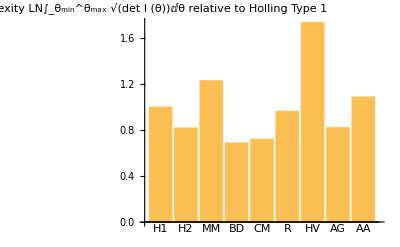

```mathematica
BarChart[NInts/NInts[[1]],ChartLabels->{"H1","H2","MM","BD","CM","R","HV","AG","AA"},
AxesLabel->"Complexity LN∫_θ_min^θ_max √(det I (θ))ⅆθ relative to Holling Type 1"]
```

```mathematica
(*
Manipulate[
ParmRange={{a,amin,amax},{h,hmin,hmax},{γ,γmin,γmax},{m,mmin,mmax},{β,βmin,βmax}};
NInts={
Log[NIntegrate[Sqrt[DetH1],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetH2],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetMM],ParmRange[[1]],ParmRange[[5]]]],
Log[NIntegrate[Sqrt[DetBD],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetCM],ParmRange[[1]],ParmRange[[2]],ParmRange[[3]]]],
Log[NIntegrate[Sqrt[DetR],ParmRange[[1]]]],
Log[NIntegrate[Sqrt[DetHV],ParmRange[[1]],ParmRange[[4]]]],
Log[NIntegrate[Sqrt[DetAG],ParmRange[[1]],ParmRange[[2]]]],
Log[NIntegrate[Sqrt[DetAA],ParmRange[[1]],ParmRange[[2]],ParmRange[[4]]]]
};
BarChart[NInts/NInts[[1]],ChartLabels->{"H1","H2","BD","CM","R","HV","AG","AA"},
AxesLabel->"Complexity relative to Holling Type 1"]
,
{{amin,0.01},0.0001,.01},
{{amax,30},1,100},
{{hmin,0.01},0.0001,0.01},
{hmax,2,100},
{{γmin,0.01},0.0001,0.01},
{γmax,2,100},
{{mmin,0.01},0.0001,0.01},
{mmax,1,100},
{{βmin,0.01},0.0001,0.01},
{βmax,1,100}
]
*)
```

#### Integrate symbolically

```mathematica
Sqrt[DetH1]
IntH1=Log[Integrate[Sqrt[DetH1],a]]//FullSimplify
```

3/2 √7 √(1/a)

-1/2 Log[1/(63 a)]

```mathematica
Sqrt[DetH2]
IntH2=Log[Integrate[Sqrt[DetH2],a,h]]//FullSimplify
```

57/2 √5 √(a^2/((1+a h)^3 (1+20 a h)^3))

Log[-(6 √5 a)/(19 h (1+a h) √(a^2/((1+a h)^3 (1+20 a h)^3)) (1+20 a h))]

```mathematica
Sqrt[DetMM]
IntMM=Log[Integrate[Sqrt[DetMM],a,β]]//FullSimplify
```

57/2 √5 √(1/((1+β)^3 (20+β)^3))

Log[-3/19 √5 a (1+β) (20+β) (21+2 β) √(1/((20+21 β+β^2)^3))]

```mathematica
Sqrt[DetBD];
IntBD=Log[Integrate[Sqrt[DetBD],a,h,γ]]//FullSimplify
```

$Aborted

```mathematica
Sqrt[DetCM]
IntCM=Log[Integrate[Sqrt[DetCM],a,h,γ]]//FullSimplify
```

√((a (21+40 a h) (9+30 γ+36 γ^2+16 γ^3) (-(a^2 (401+1260 a h+2400 a^2 h^2+8400 a^3 h^3)^2 (3+4 γ)^2)/(16 (1+a h)^6 (1+20 a h)^6 (1+γ)^2 (1+2 γ)^2)+(a^2 (21+120 a h+1260 a^2 h^2+8020 a^3 h^3) (8001+24060 a h+25200 a^2 h^2+16000 a^3 h^3) (3+4 γ)^2)/(16 (1+a h)^6 (1+20 a h)^6 (1+γ)^2 (1+2 γ)^2)))/(4 (1+a h) (1+20 a h) (1+γ)^3 (1+2 γ)^3)-(a^2 (401+840 a h+800 a^2 h^2) (5+12 γ+8 γ^2) ((a (401+840 a h+800 a^2 h^2) (21+120 a h+1260 a^2 h^2+8020 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)-(a (21+80 a h+420 a^2 h^2) (401+1260 a h+2400 a^2 h^2+8400 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2)-((21+80 a h+420 a^2 h^2) (5+12 γ+8 γ^2) (-(a^3 (401+840 a h+800 a^2 h^2) (401+1260 a h+2400 a^2 h^2+8400 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)+(a^3 (21+80 a h+420 a^2 h^2) (8001+24060 a h+25200 a^2 h^2+16000 a^3 h^3) (3+4 γ) (5+12 γ+8 γ^2))/(16 (1+a h)^5 (1+20 a h)^5 (1+γ)^3 (1+2 γ)^3)))/(4 (1+a h)^2 (1+20 a h)^2 (1+γ)^2 (1+2 γ)^2))

$Aborted

```mathematica
Sqrt[DetR]
IntR=Log[Integrate[Sqrt[DetR],a]]//FullSimplify
```

√(21/2) √(1/a)

-1/2 Log[1/(42 a)]

```mathematica
Sqrt[DetHV]
IntHV=Log[Integrate[Sqrt[DetHV],a,m]]//FullSimplify
```

21 √(2^(-3-m)) Log[2]

Log[-21 √(2^(-1-m)) a]

```mathematica
Sqrt[DetAA];
IntAG=Log[Integrate[Sqrt[DetAG],a,h]]//FullSimplify
```

$Aborted

```mathematica
Sqrt[DetAA];
IntAA=Log[Integrate[Sqrt[DetAA],a,h,m]]//FullSimplify
```

```mathematica
Ints={ΝVals,Pvals,IntH1,IntH2,IntMM,IntBD,IntCM,IntR,IntHV,IntAG,IntAA};
```

{-1/2 Log[1/(75 a)],IntH2,IntBD,IntCM,IntR,IntHV,IntAG,IntAA}

```mathematica
Export["Integrations_Symbolic.txt",Ints]
```

Integrations_Symbolic.txt